```mathematica
(*Galactic Dynamics by Binney and Tremaine pg. 46*)
```

```mathematica
Clear["Global`*"]
Needs["VectorAnalysis`"]
```

```mathematica
SetCoordinates[Cylindrical];
```

```mathematica
Cylindrical[Rr,Ttheta,Zz];
```

```mathematica
S=√(Rr^2+Zz^2+a (a+2 √(Zz^2+b^2)));
```

```mathematica
Subscript[Φ, M]=-(G M)/S;
```

```mathematica
ρ=Laplacian[Subscript[Φ, M]]/(4 Pi G)//Simplify;
```

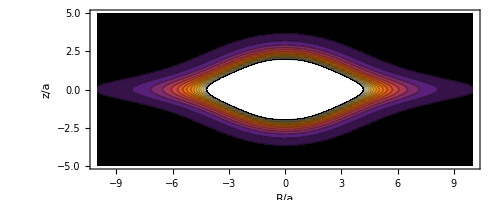

```mathematica
ContourPlot[ρ/.{a->1,b->1,M->1},{Rr,-10,10},{Zz,-5,5},Contours->18, ColorFunction->"SunsetColors",Frame->True, FrameLabel->{"R/a","z/a"},AspectRatio->1/2.5,ImageSize->{500,300}]
```